# Exploring the Inner Workings of Discrete Neural Networks

Eric Buehler
WSRP 2025

## Abstract

Neural networks, though foundational to modern artificial intelligence, often suffer from interpretability challenges due to their reliance on continuous numerical operations and gradient-based optimization methods. Discrete neural networks present an alternative that utilizes categorical elements and logic gates (AND, OR, XOR) structured within discrete, hexagonal cells. This work explores the properties and potential of discrete neural networks, highlighting how their structure influences modeling capabilities across various function types. Employing a genetic-inspired simulated annealing algorithm, the study circumvents the limitations of traditional backpropagation, offering a unique perspective on optimizing discrete architectures. The analysis underscores distinct structural patterns in these networks, providing clarity and interpretability. Future directions include extending the analysis to broader function categories, deepening structural examinations, and refining optimization methods.

## Introduction

While neural networks today are a fundamental building block of artificial intelligence (AI), their inner workings remain notoriously opaque. As AI models increasingly permeate our daily lives, from healthcare to finance, understanding and interpreting their decision-making processes becomes critical. Traditional neural networks operate primarily through continuous numerical methods, relying heavily on learned weights and activation functions that are adjusted through gradient-based optimization techniques like backpropagation. While powerful, these continuous methods often produce models whose inner logic can be challenging to interpret, obscuring the reasoning behind their outputs.

Discrete neural networks present an alternative approach to addressing these interpretability challenges. Unlike conventional neural networks, discrete neural networks do not utilize continuous numerical values for weights or activations. Instead, every component - including inputs, activations, weights, and even the training algorithm itself - is defined using discrete, categorical elements. Specifically, the discrete neural networks explored in this work are structured as grids composed of hexagonal “cells,” each containing a gate that implements a specific binary logical operation (such as AND, OR, XOR). These discrete gates serve as direct analogues to the continuous weights of traditional neural networks, controlling the flow and transformation of binary activations throughout the network.

This discrete representation enables not only greater transparency but also potentially deeper insights into the network’s internal mechanisms. By analyzing the patterns and structures that arise within these discrete architectures, researchers can more readily interpret and trace the reasoning pathways of neural networks, facilitating explanations of their outcomes.

#### Importing required packages

```mathematica
Import["~/Dropbox/wolfram/project/DiscreteNetUtil.wl"]
```

```mathematica
CopyFile[
File["~/Dropbox/wolfram/project/DiscreteNetUtil.wl"],
CloudObject[URLBuild[{$CloudRootDirectory,"WSRP25","DiscreteNetUtil"}]],
OverwriteTarget->True
]
```

CloudObject[https://www.wolframcloud.com/obj/ericlbuehler/WSRP25/DiscreteNetUtil]

```mathematica
SetPermissions[
CloudObject[URLBuild[{$CloudRootDirectory,"WSRP25","DiscreteNetUtil"}]],
"Public"
]
```

{All→Automatic,Owner→{Read,Write,Execute}}

Import the required utility functions:

```mathematica
CloudGet@"https://www.wolframcloud.com/obj/ericlbuehler/WSRP25/DiscreteNetUtil"
```

```mathematica
Names["DiscreteNetUtil`*"]
```

{CreateRampedWeights,DiscreteNet,DiscreteNetRealOneHot,OneHot10ToReal,RealToOneHot10,UpdateRandomWeights}

Description of the functions below. Note that all functions only deal with {AND, OR, XOR} gate types as they were found to work best.

CreateRampedWeights: create new, randomly initialized weights.
DiscreteNet: Raw, low-level forward pass.
DiscreteNetRealOneHot: High-level primary entrypoint for running the model. Handles encoding and decoding.
RealToOneHot10: Convert a real scalar on [0.0,1.0] to a one-hot vector with 10 columns (step size of 0.1).
OneHot10ToReal: Decodes raw 10 one-hot to real. This sums the output from each column to avoid arbitrary edge cases.
UpdateRandomWeights: Update a specified random number of the weights.

## Running the model

Before training the model, it is helpful to get an understanding of how it works and how it behaves. In this section we create some randomly initialized weights and then run the model. This also demonstrates creating visualizations.

Here, the `rampLength` variable controls how many for how many rows the columns increases, and then decreases. To maximize the area of the “hidden” space, this is defined as half the rows.

Define some hyperparameters:

```mathematica
rows = 24;
cols = 10;
rampLength = rows/2;
```

Next, we initialize the network’s weights:

```mathematica
weightDataRamp = CreateRampedWeights[rows, cols, rampLength];
```

Created 372 weights for ramped architecture

Finally, running the model is relatively easy:

```mathematica
output = DiscreteNetRealOneHot[0.5, weightDataRamp, 
  Visualize -> True, 
  Rows -> rows, 
  RampLength -> rampLength
];
```

The numerical output is at index 1:

```mathematica
output[[1]]
```

0

And the optional visualization is at index 2:

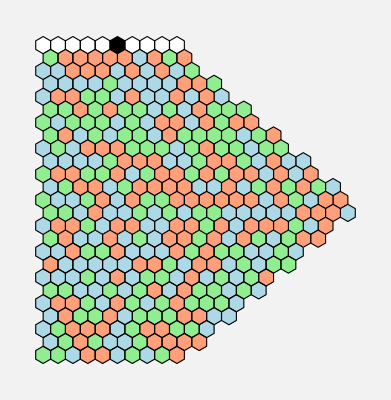

```mathematica
output[[2]]
```

## Training algorithm

During training the following genetic-style approach is used:
- run several mutated variants of the current best-performing weights as a microbatch to determine which performs best with the given loss function.
- the best-performing variant in the microbatch is used to compare against and potentially replace the running best-performing variant.
- this best-performing variant is used as the model for the next training.

To measure performance, an error value is established. This is L1 loss (maximum absolute error or MAE) and is used to define the best performing model on a linear scale.

In particular, training uses several components:
a) Learning rate: a decreasing mutation rate as training progresses. 
Because mutation rate is analogous to the learning rate in continuous machine learning, the decreasing learning rate takes inspiration from continuous machine learning. Techniques such as learning rate scheduling in continuous machine learning change the rate that the network’s weights are updated as the model trains, improving convergence.
b) Optimizer: simulated annealing
Discrete neural networks are not compatible with traditional continuous training techniques like backpropagation. While techniques like BOLD (https://arxiv.org/html/2311.07427v2) exist, they require relaxing the continuous constraint during training.
Simulated annealing works by occasionally accepting worse solutions with a certain probability. Like the continuous optimizer analogy of momentum, this helps to escape settling in local minima in the optimization landscape.
c) Random restart: restart training if progress plateaus. This serves a similar purpose as the simulated annealing algorithm, but is a far more coarse approach.
d) Penalty: due to the fact that activations in discrete neural networks are not guaranteed to reach the output, a large penalty value is applied to the error value in the case that the network does not produce an output and the expected output should have one.

Because the encoder and decoder functions are designed to return the sum of the activated outputs (0.1+0.3, for example), the model is allowed to learn more complex and flexible representations with alternative answers. As can be seen in further experiments, this is utilized by the model to enhance flexibility.

To improve performance during the training process which tests multiple mutated weights at once, we initialize parallel kernels:

```mathematica
numParallelVariants=64; 
LaunchKernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local}

In order to properly implement parallelized optimization, we must load the utilities on each parallel kernel.

```mathematica
ParallelTable[
CloudGet@"https://www.wolframcloud.com/obj/ericlbuehler/WSRP25/DiscreteNetUtil";,
{numParallelVariants}
];
```

First, can define some variables that will be used by the training loop:

```mathematica
ClearAll[weightData,weightDataNew,bestPreviousError,bestWeight,y,x,target]

bestWeight=weightData;
bestError=10^10;
currentError=bestError;
```

Next, we define training hyperparameters:

```mathematica
maxIterations=50000;
initialTemp=1.0;
finalTemp=0.001;
mutationRate=12;
minMutationRate=1;
adaptiveFactor=0.99;
restartThreshold=5000;
penaltyValue=10^6;
```

These scratch variables are used during training to track progress:

```mathematica
errorHistory={};
itersSinceImprovement=0;
```

Define the model’s shape: 24 rows ramping up and down for the first 12 and last 12 respectively. Necessarily (due to the encoding) there are 10 columns.

```mathematica
rows = 24;
cols = 10;
rampLength = rows/2;
```

Finally, create the weights for the model:

```mathematica
weightData=CreateRampedWeights[rows,cols,rampLength];
```

Created 372 weights for ramped architecture

Define the training data `x` and the target values to train against. There are multiple target data, simulating f(x) as a linear function, as an trigonometric function, and as a discrete oscillatory function:

```mathematica
x=Table[v,{v,0,1.0,0.1}];
```

```mathematica
target={0.0,0.1,0.2,0.1,0.0,0.1,0.2,0.1,0.0,0.1, 0.2};
```

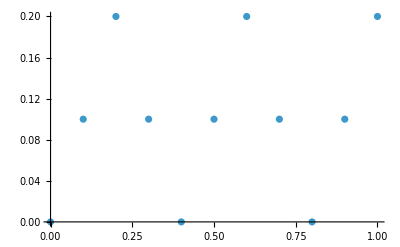

```mathematica
ListPlot[Partition[Riffle[x,target],2]]
```

This round-trip shows the target values we would expect for each `x` if the model was perfectly accurate:

```mathematica
Map[OneHot10ToReal[RealToOneHot10[#]]&,target]
```

{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}

This function wraps the network evaluation function and contains logic for evaluating the error as well as potential penalty values:

```mathematica
(*Evaluation function*)
EvaluateNetwork[weights_,x_,target_]:=Module[{y,error},
y=Map[
Module[{res=DiscreteNetRealOneHot[#,weights,Visualize->False,Rows->rows,RampLength->rampLength][[1]]},
If[res===0&&#!=0,penaltyValue,res]
]&,
x
];
error=Mean[Abs[y-target]]*10.0;
error
];
```

This implements simulated annealing where worse results are occasionally accepted to escape local minima:

```mathematica
(*Safe acceptance probability calculation*)
SafeAcceptanceProbability[deltaError_,temp_]:=Module[{arg},
arg=-deltaError/temp;
If[arg<-20,0,Exp[arg]]
];
```

Below is a walkthrough of the body of the main training loop. The entire training loop is defined as the function `TrainDiscreteNet` in the “Training Loop” section.

Define parameters describing the simulated annealing temperature as well as the current mutation rate. These define the probability that a worse solution would be accepted and the number of weights that will be mutated for each variant, respectively:

```mathematica
temp=initialTemp*(finalTemp/initialTemp)^(i/maxIterations);
currentMutationRate=Max[minMutationRate,Round[mutationRate*(adaptiveFactor^(i/1000))]];
```

Next, create several mutated variants of the current best weights. A controlled number of gates are randomly updated.

```mathematica
variants=ParallelTable[
UpdateRandomWeights[weightData,currentMutationRate],{
numParallelVariants}
];
```

Run each variant on the same inputs.

```mathematica
variantErrors=ParallelMap[
EvaluateNetwork[#,x,target]&,
variants
];
```

Find the best variant by the error to the target

```mathematica
bestVariantIndex=First[Ordering[variantErrors,1]];
weightDataNew=variants[[bestVariantIndex]];
newError=variantErrors[[bestVariantIndex]];
deltaError=newError-currentError;
```

This implements the logic to decide whether to accept. If the error is better than the penalty value and the current best is the penalty value, then always accept. However, otherwise, use the simulated annealing strategy to decide acceptance:

```mathematica
If[currentError>=penaltyValue&&newError<penaltyValue,
accept=True,
acceptProb=SafeAcceptanceProbability[deltaError,temp];
accept=deltaError<0||RandomReal[]<acceptProb
];
```

Based on the acceptance condition, we can now update the current best weight and best error:

```mathematica
If[accept,
weightData=weightDataNew;
currentError=newError;
If[newError<bestError,bestError=newError;
bestWeight=weightDataNew;
itersSinceImprovement=0;
];
];
```

Increment the counter that tracks the number of iterations since an improvement:

```mathematica
itersSinceImprovement++;
```

In the case that the network has settled in a high-error local minima, we can execute a hard restart:

```mathematica
If[itersSinceImprovement>restartThreshold,
weightData=CreateRampedWeights[rows,cols,rampLength];
currentError=EvaluateNetwork[weightData];
itersSinceImprovement=0;
];
```

This is the entirety the training algorithm.

## Training loop

```mathematica
ClearAll[TrainDiscreteNet];
```

```mathematica
TrainDiscreteNet[xs_List,target_List,OptionsPattern[{
MaxIterations->50000,
InitialTemp->1.0,
FinalTemp->0.001,
MutationRate->12,
MinMutationRate->1,
AdaptiveFactor->0.99,
RestartThreshold->5000,
Rows->24,
Cols->10,
RampLength->12,
NumParallelVariants->64,
PenaltyValue->10^6,
Seed->42}]
]:=Module[{
(*---hyper-parameters---------------------------------------*)
maxIterations=OptionValue[MaxIterations],
initialTemp=OptionValue[InitialTemp],
finalTemp=OptionValue[FinalTemp],
mutationRate=OptionValue[MutationRate],
minMutationRate=OptionValue[MinMutationRate],
adaptiveFactor=OptionValue[AdaptiveFactor],
restartThreshold=OptionValue[RestartThreshold],
rows=OptionValue[Rows],
cols=OptionValue[Cols],
rampLength=OptionValue[RampLength],
numParallelVariants=OptionValue[NumParallelVariants],
penaltyValue=OptionValue[PenaltyValue],
seed=OptionValue[Seed],
(*---state---------------------------------------------------*)
weightData,bestWeight,bestError,currentError,temp,currentMutationRate,variants,variantErrors,bestVariantIndex,weightDataNew,newError,deltaError,acceptProb,accept,errorHistory={},itersSinceImprovement=0},

(*initialise a brand-new network*)
weightData=CreateRampedWeights[rows,cols,rampLength];
bestWeight=weightData;
bestError=penaltyValue;
currentError=bestError;

SeedRandom[seed];

Do[
Print[i];
(*temperature schedule*)
temp=finalTemp+(initialTemp-finalTemp) (1-i/maxIterations);

(*mutation schedule*)
currentMutationRate=Max[minMutationRate,Round[mutationRate (adaptiveFactor^(i/1000))]];

(*generate& evaluate candidate variants in parallel*)
variants=ParallelTable[UpdateRandomWeights[weightData,currentMutationRate],{numParallelVariants}];
variantErrors=ParallelMap[EvaluateNetwork[#,xs,target]&,variants];

(*pick the best candidate*)
bestVariantIndex=First[Ordering[variantErrors,1]];
weightDataNew=variants[[bestVariantIndex]];
newError=variantErrors[[bestVariantIndex]];
deltaError=newError-currentError;

(*acceptance rule (simulated annealing)*)
accept=False;
If[currentError>=penaltyValue&&newError<penaltyValue,accept=True,acceptProb=SafeAcceptanceProbability[deltaError,temp];
accept=deltaError<0||RandomReal[]<acceptProb];

(*update incumbent solution if accepted*)
If[accept,weightData=weightDataNew;
currentError=newError;
If[newError<bestError,bestError=newError;
bestWeight=weightDataNew;
itersSinceImprovement=0;
];
];

(*restart logic for stagnation*)
itersSinceImprovement++;

If[itersSinceImprovement>restartThreshold,
weightData=CreateRampedWeights[rows,cols,rampLength];
currentError=EvaluateNetwork[weightData];
itersSinceImprovement=0;
];

(*book-keeping every 10 iters*)
If[Mod[i,10]==0&&bestError<penaltyValue,
Print[bestError];
AppendTo[errorHistory,bestError];
];,

{i,1,maxIterations}
];
<|"BestWeight"->bestWeight,"BestError"->bestError,"ErrorHistory"->errorHistory|>
];
```

## Exploring what functions are best modelled with model size vs function type

In this section, the exploration aims to identify which kinds of functions can be effectively captured by discrete neural networks of various sizes. The objective is to understand the relationship between the complexity of the target function and the size of the discrete neural network required to model it. By systematically varying the model size—characterized by the number of discrete logical gates—we observe how accurately networks can represent different categories of functions, including linear, cyclic, and trigonometric patterns. This experiment provides insight into the minimal complexity required for reliable function approximation, potentially revealing inherent trade-offs between model size and accuracy in discrete neural networks.

Initialize and install the required paclets.

```mathematica
pacletSiteURL="https://wolfram-wcs-wss-paclets.s3.amazonaws.com/PacletServer";
PacletSiteRegister[pacletSiteURL];

$WCSBatchPaclets={"WCSClient","BatchComputationProvider_WolframBatch"};
$RequiredPaclets=Join[{"RemoteBatchSubmit","CloudObject"},$WCSBatchPaclets];

installBatchPaclets[] :=
(
Print["Installing Wolfram Compute Services paclets:"];
PacletSiteUpdate[pacletSiteURL];
Do[
Print["∘ Installing ",paclet];
Replace[SelectFirst[PacletFindRemote[paclet],p|->p["Location"]===pacletSiteURL],{
p_PacletObject:>PacletInstall[p,ForceVersionInstall->True],
_:>(
Print["Trouble loading ",paclet, " paclet from remote site."];
$Failed
)
}],
{paclet,$RequiredPaclets}
];
Print[Panel[Style["Please restart Wolfram for Desktop before proceeding.",Medium,Bold],Background->Lighter[Gray, 0.8]]]
)

(* install the first time *)
If[Union[Map[Head[First[Information[PacletObject[#]]]]&,$WCSBatchPaclets]]=!={Association},
installBatchPaclets[]
]
```

These next few cells allow you to check if you are connected.

```mathematica
CloudConnect[]
```

ericlbuehler@gmail.com

```mathematica
$DefaultRemoteBatchSubmissionEnvironment
```

RemoteBatchSubmissionEnvironment[…]

```mathematica
$ServiceCreditsAvailable
```

1035

Now, we create the various target functions to model.

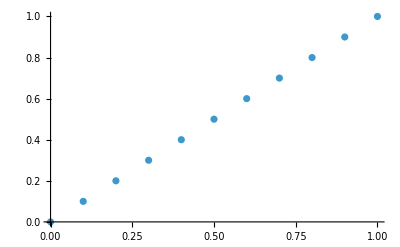

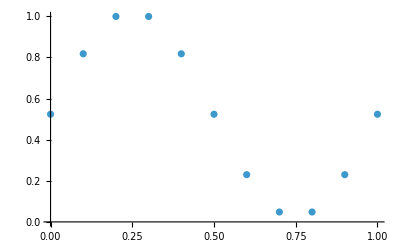

-Graphics-

```mathematica
x=Table[v,{v,0,1.0,0.1}];
targetLinear=Table[v,{v,0,1.0,0.1}];
targetTrig=Map[0.5*Sin[2Pi#]+Pi/6&,x];
targetOsc={0.0,0.1,0.2,0.1,0.0,0.1,0.2,0.1,0.0,0.1, 0.2};
ListPlot[Partition[Riffle[x,targetLinear],2]]
ListPlot[Partition[Riffle[x,targetTrig],2]]
ListPlot[Partition[Riffle[x,targetOsc],2]]
```

Here we define 4 network configurations.

```mathematica
rowsRampLengths={{24,12},{20,10},{16,8},{14,7}}
```

{{24,12},{20,10},{16,8},{14,7}}

Create the grid to train for each.

```mathematica
grid=Tuples[{rowsRampLengths,{targetLinear,targetOsc,targetTrig}}]
```

{{{24,12},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}},{{24,12},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}},{{24,12},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}},{{20,10},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}},{{20,10},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}},{{20,10},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}},{{16,8},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}},{{16,8},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}},{{16,8},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}},{{14,7},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}},{{14,7},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}},{{14,7},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}}}

This grid has 12 configurations: 4 network and 3 functions.

```mathematica
Length@grid
```

12

The grid looks like the following.

```mathematica
Scan[
rows=#[[1,1]];rampLength=#[[1,2]];target=#[[2]];Print[ToString[rows]<>" "<>ToString[rampLength]<>" "<>ToString[target]];&,
grid
]
```

24 12 {0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.}

24 12 {0., 0.1, 0.2, 0.1, 0., 0.1, 0.2, 0.1, 0., 0.1, 0.2}

24 12 {0.523599, 0.817491, 0.999127, 0.999127, 0.817491, 0.523599, 0.229706, 0.0480705, 0.0480705, 0.229706, 0.523599}

20 10 {0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.}

20 10 {0., 0.1, 0.2, 0.1, 0., 0.1, 0.2, 0.1, 0., 0.1, 0.2}

20 10 {0.523599, 0.817491, 0.999127, 0.999127, 0.817491, 0.523599, 0.229706, 0.0480705, 0.0480705, 0.229706, 0.523599}

16 8 {0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.}

16 8 {0., 0.1, 0.2, 0.1, 0., 0.1, 0.2, 0.1, 0., 0.1, 0.2}

16 8 {0.523599, 0.817491, 0.999127, 0.999127, 0.817491, 0.523599, 0.229706, 0.0480705, 0.0480705, 0.229706, 0.523599}

14 7 {0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.}

14 7 {0., 0.1, 0.2, 0.1, 0., 0.1, 0.2, 0.1, 0., 0.1, 0.2}

14 7 {0.523599, 0.817491, 0.999127, 0.999127, 0.817491, 0.523599, 0.229706, 0.0480705, 0.0480705, 0.229706, 0.523599}

This function handles dispatching the batch run.

```mathematica
LaunchTrainingRun[rows_,rampLength_,x_,target_]:=Module[{},
RemoteBatchSubmit[
ParallelTable[
CloudGet@"https://www.wolframcloud.com/obj/ericlbuehler/WSRP25/DiscreteNetUtil";,
{numParallelVariants}
];
TrainDiscreteNet[x,target,Rows->rows,RampLength->rampLength,MaxIterations->250]
]
(*TrainDiscreteNet[x,target,Rows->rows,RampLength->rampLength,MaxIterations->250]*)
];
```

```mathematica
x
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

Launch the training run:

```mathematica
jobs=Map[
Function[gridEntry,
rows=gridEntry[[1,1]];
rampLength=gridEntry[[1,2]];
target=gridEntry[[2]];
(*Print[ToString[rows]<>" "<>ToString[rampLength]<>" "<>ToString[target]];*)
LaunchTrainingRun[rows,rampLength,x,target]
],
grid
];
```

```mathematica
jobs
```

{RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…]}

While running the job, you can check the status.

```mathematica
Map[#["JobStatus"]&,jobs]
```

{Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded,Succeeded}

Or, you can check the log for a more detailed status.

```mathematica
Map[#["JobLog"]&,jobs]
```

Once the job is done, we extract the results into a list.

```mathematica
results= Map[#["EvaluationResult"]&,jobs]
```

The most important result is the final error value.

```mathematica
errors = Map[#["BestError"]&,results]
```

{1000000,0.454545,0.705819,0.454545,0.363636,0.91944,0.454545,0.454545,0.956338,0.454545,0.545455,1.28817}

To compare the final error value with the model’s training configuration, we can map them together.

```mathematica
pairedResults=Transpose@{errors,grid}
```

{{1000000,{{24,12},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}}},{0.454545,{{24,12},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}}},{0.705819,{{24,12},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}}},{0.454545,{{20,10},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}}},{0.363636,{{20,10},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}}},{0.91944,{{20,10},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}}},{0.454545,{{16,8},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}}},{0.454545,{{16,8},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}}},{0.956338,{{16,8},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}}},{0.454545,{{14,7},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}}},{0.545455,{{14,7},{0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2}}},{1.28817,{{14,7},{0.523599,0.817491,0.999127,0.999127,0.817491,0.523599,0.229706,0.0480705,0.0480705,0.229706,0.523599}}}}

Now, we can process the paired results to generate a graph and understand the best configuration of the network for each dataset!

```mathematica
processedData=Map[
Function[result,<|"Error"->result[[1]],"ModelSize"->result[[2,1]],"ModelRows"->result[[2,1,1]],"TargetData"->result[[2,2]]|>],
pairedResults
];
```

We can delete duplicate target data patterns so that we are only grouping by meaningful data.

```mathematica
targetPatterns=DeleteDuplicates[processedData[[All,"TargetData"]]];
```

Next, we create labels for each of these target patterns.

```mathematica
labelFor[pattern_]:=Which[
pattern==={0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},
"Linear (0 to 1)",
pattern==={0.,0.1,0.2,0.1,0.,0.1,0.2,0.1,0.,0.1,0.2},
"Cyclic (0-0.1-0.2)",
MatchQ[pattern[[1]],_?NumericQ]&&pattern[[1]]>0.5,
"Trigonometric",
True,ToString[pattern]
];
```

Group data by target pattern

```mathematica
groupedData=GroupBy[processedData,#["TargetData"]&];
```

Get the 3 target patterns:

```mathematica
patterns=Keys[groupedData];
```

Create a visualization for each grouping of target data to model size:

```mathematica
chartData=Table[With[{patternData=groupedData[p]},
Labeled[
ListPlot[
Map[{#["ModelRows"],#["Error"]}&,patternData],
PlotStyle->{PointSize[0.02],ColorData[97][row]},
PlotMarkers->{Automatic,15},
PlotRange->{{10,26},{0,1.4}},
Frame->True,
FrameLabel->{"Model size (rows)","Error (L1)"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thin],
ImageSize->250
],
labelFor[p],
Top
]
],
{p,patterns}
];
```

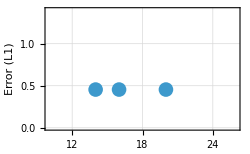
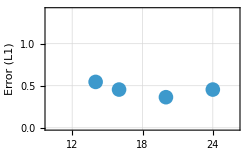
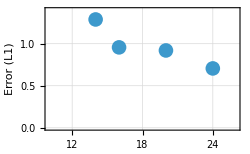
{-Graphics-Linear (0 to 1),-Graphics-Cyclic (0-0.1-0.2),-Graphics-Trigonometric}

```mathematica
chartData
```

The completed scatter plots reveal a clear capacity ladder.

Errors for the linear task collapse below 0.4 once the model reaches ~20 rows and flatten thereafter.

Cyclic (sawtooth) tasks tolerate roughly five fewer rows of under-fit before crossing the same threshold.

The trigonometric task falls in between: its smoothness eases approximation, yet its periodicity still needs more capacity than the linear baseline but less than the staircase.

Across all three patterns, additional width beyond ~20 rows typically yields diminishing returns, marking that band as the practical sweet-spot for subsequent experiments. The key outlier is the trigonometric task which performs better as the model size increases. This could be due to the increased task complexity.

The results clearly highlight a pattern where specific functions inherently require different minimal network sizes to achieve low error. For simpler functions, like linear patterns, smaller models perform adequately, maintaining low error rates. However, more complex functions—such as those exhibiting cyclic or trigonometric behavior—show a steep increase in error when modeled by smaller networks, indicating the necessity of larger, more complex architectures for accurate representation. This exploration underscores the importance of carefully matching model size to the type of function, affirming that discrete neural networks’ capacities strongly correlate with both structural complexity and the intrinsic characteristics of the functions they approximate.

## Exploring if discrete neural networks’ weights reflect their functions

This section investigates whether discrete neural networks, after successfully learning to represent a given function, reflect identifiable patterns within their learned weights. Specifically, we analyze discrete weights represented by logical gates (such as AND, OR, and XOR gates) to detect systematic structures correlated with the functions they model. By visually and computationally inspecting these weight patterns, the exploration seeks to uncover if specific gate distributions emerge consistently for certain types of functions. Such insight would confirm that discrete neural networks not only memorize input-output relationships but also encode meaningful structural characteristics inherent to their learned tasks.

First, we create our input data.

```mathematica
x=Table[x,{x,0.0,0.9,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}

Then, we create a very simple stepped set of target values.

```mathematica
target={0.0,0.0,0.0,0.0,0.0,1.0,1.0,1.0,1.0,1.0}
```

{0.,0.,0.,0.,0.,1.,1.,1.,1.,1.}

This forms a very simple piecewise function with a distinctive step.

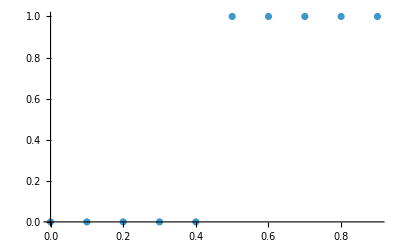

```mathematica
ListPlot[Partition[Riffle[x,target],2]]
```

We can now train a discrete neural network:

```mathematica
TrainDiscreteNet[x, target,MaxIterations->50]
```

<|BestWeight→{AND,XOR,AND,OR,AND,OR,OR,OR,OR,AND,OR,OR,OR,XOR,AND,AND,OR,XOR,OR,OR,XOR,XOR,XOR,OR,AND,XOR,AND,XOR,XOR,AND,AND,AND,OR,OR,XOR,XOR,XOR,XOR,XOR,OR,OR,OR,XOR,AND,AND,XOR,AND,OR,OR,XOR,OR,XOR,XOR,XOR,OR,AND,AND,OR,XOR,OR,XOR,OR,XOR,XOR,AND,AND,OR,AND,OR,AND,AND,XOR,OR,XOR,XOR,XOR,OR,XOR,AND,AND,OR,AND,XOR,XOR,OR,OR,AND,OR,XOR,AND,AND,XOR,AND,XOR,XOR,AND,XOR,AND,XOR,AND,OR,AND,OR,XOR,XOR,AND,OR,OR,XOR,OR,OR,XOR,XOR,OR,XOR,OR,XOR,AND,AND,OR,AND,XOR,XOR,XOR,OR,AND,OR,XOR,OR,AND,XOR,OR,OR,OR,AND,OR,OR,XOR,XOR,XOR,XOR,OR,OR,AND,XOR,OR,XOR,OR,AND,OR,XOR,AND,XOR,OR,OR,XOR,XOR,AND,XOR,AND,OR,AND,AND,OR,XOR,AND,XOR,XOR,XOR,XOR,AND,XOR,XOR,XOR,AND,OR,XOR,AND,OR,AND,OR,AND,AND,OR,XOR,XOR,AND,XOR,XOR,OR,XOR,OR,OR,OR,XOR,XOR,XOR,XOR,AND,OR,OR,XOR,OR,AND,AND,OR,OR,AND,XOR,AND,OR,AND,AND,XOR,XOR,AND,OR,OR,XOR,OR,OR,OR,XOR,OR,XOR,XOR,OR,OR,AND,OR,OR,AND,AND,OR,OR,XOR,XOR,OR,AND,XOR,AND,AND,AND,XOR,OR,AND,XOR,XOR,XOR,XOR,OR,AND,XOR,OR,OR,AND,XOR,OR,OR,OR,AND,OR,AND,AND,OR,XOR,XOR,XOR,AND,OR,AND,AND,AND,XOR,XOR,XOR,AND,OR,OR,OR,OR,OR,XOR,XOR,OR,AND,AND,AND,AND,XOR,XOR,OR,OR,XOR,XOR,AND,AND,AND,XOR,AND,AND,AND,OR,XOR,OR,AND,XOR,AND,AND,OR,OR,XOR,XOR,AND,OR,AND,XOR,AND,OR,OR,AND,XOR,XOR,OR,XOR,XOR,OR,OR,AND,OR,AND,XOR,AND,OR,AND,XOR,AND,OR,AND,XOR,AND,OR,OR,AND,OR,AND,OR,OR,XOR,OR,AND,AND,AND,XOR,AND,OR,AND,OR,AND,AND,XOR,OR,AND,XOR,XOR,AND,OR,OR,AND,XOR,AND,AND},BestError→0.,ErrorHistory→{1.3,0.9,0.7,0.,0.}|>

```mathematica
result=<|"BestWeight"->{"AND","XOR","AND","OR","AND","OR","OR","OR","OR","AND","OR","OR","OR","XOR","AND","AND","OR","XOR","OR","OR","XOR","XOR","XOR","OR","AND","XOR","AND","XOR","XOR","AND","AND","AND","OR","OR","XOR","XOR","XOR","XOR","XOR","OR","OR","OR","XOR","AND","AND","XOR","AND","OR","OR","XOR","OR","XOR","XOR","XOR","OR","AND","AND","OR","XOR","OR","XOR","OR","XOR","XOR","AND","AND","OR","AND","OR","AND","AND","XOR","OR","XOR","XOR","XOR","OR","XOR","AND","AND","OR","AND","XOR","XOR","OR","OR","AND","OR","XOR","AND","AND","XOR","AND","XOR","XOR","AND","XOR","AND","XOR","AND","OR","AND","OR","XOR","XOR","AND","OR","OR","XOR","OR","OR","XOR","XOR","OR","XOR","OR","XOR","AND","AND","OR","AND","XOR","XOR","XOR","OR","AND","OR","XOR","OR","AND","XOR","OR","OR","OR","AND","OR","OR","XOR","XOR","XOR","XOR","OR","OR","AND","XOR","OR","XOR","OR","AND","OR","XOR","AND","XOR","OR","OR","XOR","XOR","AND","XOR","AND","OR","AND","AND","OR","XOR","AND","XOR","XOR","XOR","XOR","AND","XOR","XOR","XOR","AND","OR","XOR","AND","OR","AND","OR","AND","AND","OR","XOR","XOR","AND","XOR","XOR","OR","XOR","OR","OR","OR","XOR","XOR","XOR","XOR","AND","OR","OR","XOR","OR","AND","AND","OR","OR","AND","XOR","AND","OR","AND","AND","XOR","XOR","AND","OR","OR","XOR","OR","OR","OR","XOR","OR","XOR","XOR","OR","OR","AND","OR","OR","AND","AND","OR","OR","XOR","XOR","OR","AND","XOR","AND","AND","AND","XOR","OR","AND","XOR","XOR","XOR","XOR","OR","AND","XOR","OR","OR","AND","XOR","OR","OR","OR","AND","OR","AND","AND","OR","XOR","XOR","XOR","AND","OR","AND","AND","AND","XOR","XOR","XOR","AND","OR","OR","OR","OR","OR","XOR","XOR","OR","AND","AND","AND","AND","XOR","XOR","OR","OR","XOR","XOR","AND","AND","AND","XOR","AND","AND","AND","OR","XOR","OR","AND","XOR","AND","AND","OR","OR","XOR","XOR","AND","OR","AND","XOR","AND","OR","OR","AND","XOR","XOR","OR","XOR","XOR","OR","OR","AND","OR","AND","XOR","AND","OR","AND","XOR","AND","OR","AND","XOR","AND","OR","OR","AND","OR","AND","OR","OR","XOR","OR","AND","AND","AND","XOR","AND","OR","AND","OR","AND","AND","XOR","OR","AND","XOR","XOR","AND","OR","OR","AND","XOR","AND","AND"},"BestError"->0.,"ErrorHistory"->{1.3,0.8999999999999999,0.7000000000000007,0.0,0.0}|>;
```

```mathematica
Manipulate[DiscreteNetRealOneHot[x, result["BestWeight"], 
  Visualize -> True, 
  Rows -> 24, 
  RampLength -> 12
],{{x,0.1},0.0,1.0}]
```

This interactive visualization clearly illustrates striking patterns within the trained discrete neural network. For each distinct output value (0.0 and 1.0) the model exhibits a highly structured internal behavior. After an initial series of rows characterized by dynamic gate switching, the network consistently settles into a stable, fixed logical path, indicating that these early rows effectively serve as adaptive routing mechanisms directing inputs into predictable, stable computational pathways.

An intriguing example of emergent behavior occurs when representing the 1.0 output: rather than directly activating the cell labeled explicitly for “1.0,” the network cleverly combines activations from “0.2” and “0.8” cells. This phenomenon shows that discrete neural networks do not merely encode memorized input-output mappings; instead, they form a computational narrative, transparently revealing the internal logic and mechanisms behind the function the network implements.

## Conclusion and Next Steps

We have demonstrated that discrete neural networks exhibit distinct patterns in how their complexity and internal structure correlate with their ability to model various classes of functions. The analysis of network size versus performance across linear, cyclic, and trigonometric functions highlighted critical insights: larger networks generally improved modeling capabilities, yet the relationship varied notably across function types. Furthermore, visualizations of network weights provided clear indications that discrete neural networks encode functional characteristics distinctly within their structural parameters.

Additionally, the genetic-inspired simulated annealing training algorithm employed offers significant advantages over traditional backpropagation methods. Since discrete neural networks rely on logic gate structures (AND, OR, XOR) rather than differentiable activation functions, standard gradient-based optimization techniques like backpropagation are infeasible. The simulated annealing approach effectively navigates the non-differentiable landscape by exploring a broader range of network configurations, thus optimizing the discrete structures directly without the need for gradient information.

Moving forward, several promising directions warrant further exploration:

1) Expanded Function Set Analysis: Investigating additional function categories, such as exponential, logarithmic, or piecewise-defined functions, will clarify the broader applicability of discrete neural networks.
2) Deeper Structural Analysis: Performing more detailed and systematic weight pattern analyses using quantitative metrics and advanced visualization techniques can help better understand the intrinsic encoding mechanisms of discrete neural networks.
3) Optimization and Generalization: Evaluating methods that enhance generalization, such as modified genetic algorithms or hybrid training approaches, will further refine the practical applicability of discrete neural networks in modeling complex functions.

These next steps will build upon the findings presented here, guiding future research toward a deeper theoretical understanding and improved practical implementations of discrete neural network models.

## References

Wolfram, S. (2024, August 22). What’s really going on in machine learning? Some minimal models. Stephen Wolfram Writings. Retrieved July 9, 2025, from https://writings.stephenwolfram.com/2024/08/whats-really-going-on-in-machine-learning-some-minimal-models/